```mathematica
Needs["Notation`"]
```

```mathematica
Notation[Subscript[V, pdσ] ⟺ pds]
Notation[Subscript[V, pdπ] ⟺ pdpi]
```

```mathematica
(*** we write out the hopping integral of p and d orbitals**)
```

```mathematica
(* pxdxy *)
```

```mathematica
pxdxy = √3 l^2 m pds+ m(1-2l^2) pdpi
```

(1-2 l^2) m V_pdπ+√3 l^2 m V_pdσ

```mathematica
(* pxdyz *)
```

```mathematica
pxdyz = √3 l*m*n pds-2 l*m*n pdpi
```

-2 l m n V_pdπ+√3 l m n V_pdσ

```mathematica
(* pxdzx *)
```

```mathematica
pxdzx = √3 l^2n pds+n(1-2l^2) pdpi
```

(1-2 l^2) n V_pdπ+√3 l^2 n V_pdσ

```mathematica
(* pxdx^2-y^2 *)
```

```mathematica
pxdx2= √3/2 (l(l^2-m^2)) pds+l(1-l^2+m^2) pdpi
```

l (1-l^2+m^2) V_pdπ+1/2 √3 l (l^2-m^2) V_pdσ

```mathematica
(* pxdz^2 *)
```

```mathematica
pxdz2= l(n^2-0.5(l^2+m^2)) pds-√3 l(n^2) pdpi
```

-√3 l n^2 V_pdπ+l (-0.5 (l^2+m^2)+n^2) V_pdσ

```mathematica
(* pzdxy *)
pzdxy = √3 n*l* m pds-2*l*m*n pdpi
```

-2 l m n V_pdπ+√3 l m n V_pdσ

```mathematica
(* pzdyz *)
```

```mathematica
pzdyz = √3 n*m*n pds+m(1-2n^2) pdpi
```

m (1-2 n^2) V_pdπ+√3 m n^2 V_pdσ

```mathematica
(* pzdzx *)
```

```mathematica
pzdzx = √3 n^2l pds+l(1-2n^2) pdpi
```

l (1-2 n^2) V_pdπ+√3 l n^2 V_pdσ

```mathematica
(* pzdx^2 *)
pzdx2 = √3/2 (n(l^2-m^2)) pds-n(l^2-m^2) pdpi
```

-(l^2-m^2) n V_pdπ+1/2 √3 (l^2-m^2) n V_pdσ

```mathematica
(* pzdz^2 *)
```

```mathematica
pzdz2 = n(n^2-0.5(l^2+m^2)) pds+√3 n(l^2+m^2) pdpi
```

√3 (l^2+m^2) n V_pdπ+n (-0.5 (l^2+m^2)+n^2) V_pdσ

```mathematica
(* pydxy *)
pydxy = √3 m^2l*pds + l(1-2m^2)pdpi
```

l (1-2 m^2) V_pdπ+√3 l m^2 V_pdσ

```mathematica
(* pydyz *)
```

```mathematica
pydyz = √3 m^2n*pds + n(1-2m^2)pdpi
```

(1-2 m^2) n V_pdπ+√3 m^2 n V_pdσ

```mathematica
(* pydzx *)
pydzx = √3 l*m*n*pds - 2*l*m*n*pdpi
```

-2 l m n V_pdπ+√3 l m n V_pdσ

```mathematica
(* pydx^2 *)
```

```mathematica
pydx2 = √3/2 (m(l^2-m^2)) pds-m(1+l^2-m^2) pdpi
```

-m (1+l^2-m^2) V_pdπ+1/2 √3 m (l^2-m^2) V_pdσ

```mathematica
(* pydz^2 *)
```

```mathematica
pydz2 = m(n^2-0.5*(l^2+m^2)) pds-√3(m*n^2) pdpi
```

-√3 m n^2 V_pdπ+m (-0.5 (l^2+m^2)+n^2) V_pdσ

```mathematica
pdtable = Table[0,{i,1,4},{j,1,6}]
```

{{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}}

```mathematica
pdtable[[1,1]]=t;
pdtable[[2,1]]="px";
pdtable[[3,1]]="py";
pdtable[[4,1]]="pz";
pdtable[[1,2]]="dxy";
pdtable[[1,3]]="dyz";
pdtable[[1,4]]="dzx";
pdtable[[1,5]]="dx2";
pdtable[[1,6]]="dz2";
pdtable[[2,2]]=pxdxy;
pdtable[[2,3]]=pxdyz;
pdtable[[2,4]]=pxdzx;
pdtable[[2,5]]=pxdx2;
pdtable[[2,6]]=pxdz2;
pdtable[[3,2]]=pydxy;
pdtable[[3,3]]=pydyz;
pdtable[[3,4]]=pydzx;
pdtable[[3,5]]=pydx2;
pdtable[[3,6]]=pydz2;
pdtable[[4,2]]=pzdxy;
pdtable[[4,3]]=pzdyz;
pdtable[[4,4]]=pzdzx;
pdtable[[4,5]]=pzdx2;
pdtable[[4,6]]=pzdz2; 
TableForm[pdtable]
```

t | dxy | dyz | dzx | dx2 | dz2
px | (1-2 l^2) m V_pdπ+√3 l^2 m V_pdσ | -2 l m n V_pdπ+√3 l m n V_pdσ | (1-2 l^2) n V_pdπ+√3 l^2 n V_pdσ | l (1-l^2+m^2) V_pdπ+1/2 √3 l (l^2-m^2) V_pdσ | -√3 l n^2 V_pdπ+l (-0.5 (l^2+m^2)+n^2) V_pdσ
py | l (1-2 m^2) V_pdπ+√3 l m^2 V_pdσ | (1-2 m^2) n V_pdπ+√3 m^2 n V_pdσ | -2 l m n V_pdπ+√3 l m n V_pdσ | -m (1+l^2-m^2) V_pdπ+1/2 √3 m (l^2-m^2) V_pdσ | -√3 m n^2 V_pdπ+m (-0.5 (l^2+m^2)+n^2) V_pdσ
pz | -2 l m n V_pdπ+√3 l m n V_pdσ | m (1-2 n^2) V_pdπ+√3 m n^2 V_pdσ | l (1-2 n^2) V_pdπ+√3 l n^2 V_pdσ | -(l^2-m^2) n V_pdπ+1/2 √3 (l^2-m^2) n V_pdσ | √3 (l^2+m^2) n V_pdπ+n (-0.5 (l^2+m^2)+n^2) V_pdσ

```mathematica
(*180-bond*)
```

```mathematica
td1={l->-1,m->0,n->0}
```

{l→-1,m→0,n→0}

```mathematica
TableForm[pdtable//.td1]
```

t | dxy | dyz | dzx | dx2 | dz2
px | 0 | 0 | 0 | -1/2 √3 V_pdσ | 0.5 V_pdσ
py | -V_pdπ | 0 | 0 | 0 | 0.
pz | 0 | 0 | -V_pdπ | 0 | 0.

```mathematica
(* 90-bond *)
```

```mathematica
td2={l->0,m->1,n->0}
```

{l→0,m→1,n→0}

```mathematica
{l->0,m->1,n->0}
TableForm[pdtable//.td2]
```

{l→0,m→1,n→0}

t | dxy | dyz | dzx | dx2 | dz2
px | V_pdπ | 0 | 0 | 0 | 0.
py | 0 | 0 | 0 | -1/2 √3 V_pdσ | -0.5 V_pdσ
pz | 0 | V_pdπ | 0 | 0 | 0.

```mathematica
pdtableleft = pdtable/.td1
```

{{t,dxy,dyz,dzx,dx2,dz2},{px,0,0,0,-1/2 √3 V_pdσ,0.5 V_pdσ},{py,-V_pdπ,0,0,0,0.},{pz,0,0,-V_pdπ,0,0.}}

```mathematica
TableForm[pdtableleft]
```

t | dxy | dyz | dzx | dx2 | dz2
px | 0 | 0 | 0 | -1/2 √3 V_pdσ | 0.5 V_pdσ
py | -V_pdπ | 0 | 0 | 0 | 0.
pz | 0 | 0 | -V_pdπ | 0 | 0.

```mathematica
pdtableright = pdtable
```

{{t,dxy,dyz,dzx,dx2,dz2},{px,(1-2 l^2) m V_pdπ+√3 l^2 m V_pdσ,-2 l m n V_pdπ+√3 l m n V_pdσ,(1-2 l^2) n V_pdπ+√3 l^2 n V_pdσ,l (1-l^2+m^2) V_pdπ+1/2 √3 l (l^2-m^2) V_pdσ,-√3 l n^2 V_pdπ+l (-0.5 (l^2+m^2)+n^2) V_pdσ},{py,l (1-2 m^2) V_pdπ+√3 l m^2 V_pdσ,(1-2 m^2) n V_pdπ+√3 m^2 n V_pdσ,-2 l m n V_pdπ+√3 l m n V_pdσ,-m (1+l^2-m^2) V_pdπ+1/2 √3 m (l^2-m^2) V_pdσ,-√3 m n^2 V_pdπ+m (-0.5 (l^2+m^2)+n^2) V_pdσ},{pz,-2 l m n V_pdπ+√3 l m n V_pdσ,m (1-2 n^2) V_pdπ+√3 m n^2 V_pdσ,l (1-2 n^2) V_pdπ+√3 l n^2 V_pdσ,-(l^2-m^2) n V_pdπ+1/2 √3 (l^2-m^2) n V_pdσ,√3 (l^2+m^2) n V_pdπ+n (-0.5 (l^2+m^2)+n^2) V_pdσ}}

```mathematica
TableForm[pdtableright]
```

t | dxy | dyz | dzx | dx2 | dz2
px | (1-2 l^2) m V_pdπ+√3 l^2 m V_pdσ | -2 l m n V_pdπ+√3 l m n V_pdσ | (1-2 l^2) n V_pdπ+√3 l^2 n V_pdσ | l (1-l^2+m^2) V_pdπ+1/2 √3 l (l^2-m^2) V_pdσ | -√3 l n^2 V_pdπ+l (-0.5 (l^2+m^2)+n^2) V_pdσ
py | l (1-2 m^2) V_pdπ+√3 l m^2 V_pdσ | (1-2 m^2) n V_pdπ+√3 m^2 n V_pdσ | -2 l m n V_pdπ+√3 l m n V_pdσ | -m (1+l^2-m^2) V_pdπ+1/2 √3 m (l^2-m^2) V_pdσ | -√3 m n^2 V_pdπ+m (-0.5 (l^2+m^2)+n^2) V_pdσ
pz | -2 l m n V_pdπ+√3 l m n V_pdσ | m (1-2 n^2) V_pdπ+√3 m n^2 V_pdσ | l (1-2 n^2) V_pdπ+√3 l n^2 V_pdσ | -(l^2-m^2) n V_pdπ+1/2 √3 (l^2-m^2) n V_pdσ | √3 (l^2+m^2) n V_pdπ+n (-0.5 (l^2+m^2)+n^2) V_pdσ

```mathematica
lefthop = pdtableleft[[2;;4,2;;6]]
```

{{0,0,0,-1/2 √3 V_pdσ,0.5 V_pdσ},{-V_pdπ,0,0,0,0.},{0,0,-V_pdπ,0,0.}}

```mathematica
righthop = pdtableright[[2;;4,2;;6]]
```

{{(1-2 l^2) m V_pdπ+√3 l^2 m V_pdσ,-2 l m n V_pdπ+√3 l m n V_pdσ,(1-2 l^2) n V_pdπ+√3 l^2 n V_pdσ,l (1-l^2+m^2) V_pdπ+1/2 √3 l (l^2-m^2) V_pdσ,-√3 l n^2 V_pdπ+l (-0.5 (l^2+m^2)+n^2) V_pdσ},{l (1-2 m^2) V_pdπ+√3 l m^2 V_pdσ,(1-2 m^2) n V_pdπ+√3 m^2 n V_pdσ,-2 l m n V_pdπ+√3 l m n V_pdσ,-m (1+l^2-m^2) V_pdπ+1/2 √3 m (l^2-m^2) V_pdσ,-√3 m n^2 V_pdπ+m (-0.5 (l^2+m^2)+n^2) V_pdσ},{-2 l m n V_pdπ+√3 l m n V_pdσ,m (1-2 n^2) V_pdπ+√3 m n^2 V_pdσ,l (1-2 n^2) V_pdπ+√3 l n^2 V_pdσ,-(l^2-m^2) n V_pdπ+1/2 √3 (l^2-m^2) n V_pdσ,√3 (l^2+m^2) n V_pdπ+n (-0.5 (l^2+m^2)+n^2) V_pdσ}}

```mathematica
(* dxy, dx2, dz2 *)
```

```mathematica
dxypxdxy = lefthop[[1,1]]righthop[[1,1]]
```

0

```mathematica
dx2pxdx2 = lefthop[[1,4]]righthop[[1,4]]
```

-1/2 √3 V_pdσ (l (1-l^2+m^2) V_pdπ+1/2 √3 l (l^2-m^2) V_pdσ)

```mathematica
dz2pxdz2 = lefthop[[1,5]]righthop[[1,5]]
```

0.5 V_pdσ (-√3 l n^2 V_pdπ+l (-0.5 (l^2+m^2)+n^2) V_pdσ)

```mathematica
dxypydxy = lefthop[[2,1]]righthop[[2,1]]
```

-V_pdπ (l (1-2 m^2) V_pdπ+√3 l m^2 V_pdσ)

```mathematica
dx2pydx2 = lefthop[[2,4]]righthop[[2,4]]
```

0

```mathematica
dz2pydz2 = lefthop[[2,5]]righthop[[2,5]]
```

0.

```mathematica
dxypzdxy = lefthop[[3,1]]righthop[[3,1]]
```

0

```mathematica
dx2pzdx2 = lefthop[[3,4]]righthop[[3,4]]
```

0

```mathematica
dz2pzdz2 = lefthop[[3,5]]righthop[[3,5]]
```

0.

```mathematica
dxypxdx2 = lefthop[[1,1]]righthop[[1,4]]
```

0

```mathematica
dxypxdz2 = lefthop[[1,1]]righthop[[1,5]]
```

0

```mathematica
dxypydx2 = lefthop[[2,1]]righthop[[2,4]]
```

-V_pdπ (-m (1+l^2-m^2) V_pdπ+1/2 √3 m (l^2-m^2) V_pdσ)

```mathematica
dxypydz2 = lefthop[[2,1]]righthop[[2,5]]
```

-V_pdπ (-√3 m n^2 V_pdπ+m (-0.5 (l^2+m^2)+n^2) V_pdσ)

```mathematica
dxypzdx2 = lefthop[[3,1]]righthop[[3,4]]
```

0

```mathematica
dxypzdz2 = lefthop[[3,1]]righthop[[3,5]]
```

0

```mathematica
td2 ={l->Cos[θ],m->Sin[θ],n->0}
```

{l→Cos[θ],m→Sin[θ],n→0}

```mathematica
t23a = dxypxdx2 + dxypydx2+dxypzdx2
```

-V_pdπ (-m (1+l^2-m^2) V_pdπ+1/2 √3 m (l^2-m^2) V_pdσ)

```mathematica
t23b = dxypxdz2+dxypydz2+dxypzdz2
```

-V_pdπ (-√3 m n^2 V_pdπ+m (-0.5 (l^2+m^2)+n^2) V_pdσ)

```mathematica
t23b//.td2
```

0.5 V_pdπ V_pdσ Sin[θ] (Cos[θ]^2+Sin[θ]^2)

```mathematica
t22 = dz2pxdz2 + dz2pydz2 + dz2pzdz2//Simplify
```

l V_pdσ (-0.866025 n^2 V_pdπ+0.5 (-0.5 (l^2+m^2)+n^2) V_pdσ)

```mathematica
t22//.td2
```

V_pdσ Cos[θ] (0.-0.25 V_pdσ (Cos[θ]^2+Sin[θ]^2))

```mathematica
t11 = dx2pxdx2+ dx2pydx2+dx2pzdx2
```

-1/2 √3 V_pdσ (l (1-l^2+m^2) V_pdπ+1/2 √3 l (l^2-m^2) V_pdσ)

```mathematica
beta = t23a/t22 /.td2/.pds->10pdpi//Simplify
```

-(0.04 Tan[θ] (-7.66025+Sec[θ]^2+7.66025 Tan[θ]^2))/(1.+Tan[θ]^2)

```mathematica
betab = t23b/t22 /.td2/.pds->10pdpi//Simplify
```

-0.2 Tan[θ]

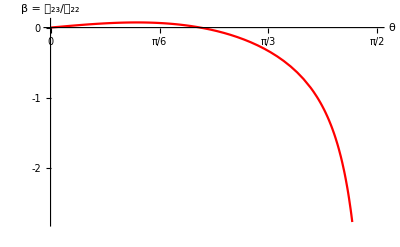

```mathematica
Plot[beta,{θ,0,π/2},Ticks->{{0,Pi/6,Pi/3,Pi/2},{-2,-1,0}},AxesLabel->{"θ","β = 𝓉_23/𝓉_22"},PlotStyle->Red]
```

```mathematica
FrameLabel
```

FrameLabel

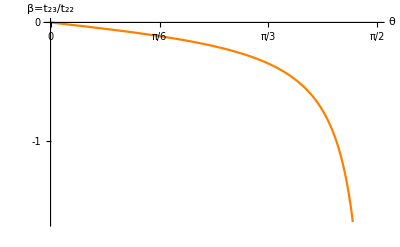

```mathematica
Plot[betab,{θ,0,π/2},Ticks->{{0,Pi/6,Pi/3,Pi/2},{-2,-1,0}},AxesLabel->{"θ","β=t_23/t_22"},PlotStyle->Orange]
```

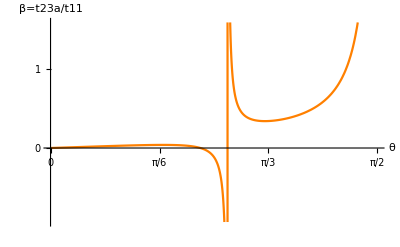

```mathematica
Plot[t23a/t11/.td2//.pds->10pdpi//Simplify,{θ,0,π/2},Ticks->{{0,Pi/6,Pi/3,Pi/2},{-2,-1,0,1,2}},AxesLabel->{"θ","β=t23a/t11"},PlotStyle->Orange]
```

```mathematica
SphericalHarmonicY
```

SphericalHarmonicY

```mathematica
SphericalPlot3D[Abs[SphericalHarmonicY[1,1,θ,ϕ]+SphericalHarmonicY[1,-1,θ,ϕ]]^2,{θ,0,π},{ϕ,0,2π},PlotRange->Full,Boxed->False,Axes->False,Mesh->None,PlotStyle->Green]
```

-Graphics3D-

```mathematica
SphericalPlot3D[Abs[SphericalHarmonicY[2,2,θ,ϕ]+SphericalHarmonicY[2,-2,θ,ϕ]]^2,{θ,0,π},{ϕ,0,2π},PlotRange->Full,Boxed->False,Axes->False,Mesh->None,PlotStyle->Green]
```

-Graphics3D-

```mathematica
SphericalPlot3D[Abs[SphericalHarmonicY[2,0,θ,ϕ]+SphericalHarmonicY[2,0,θ,ϕ]]^2,{θ,0,π},{ϕ,0,2π},PlotRange->Full,Boxed->False,Axes->False,Mesh->None,PlotStyle->Blue]
```

-Graphics3D-